```mathematica
rules={length->22/10,hight->41/100};
Ω=RegionDifference[Rectangle[{0,0},{length,hight}],Disk[{1/5,1/5},1/20]]/.rules;
```

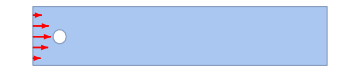

```mathematica
Show[BoundaryDiscretizeRegion[Ω],bmesh=HighlightMesh[BoundaryDiscretizeRegion[Ω,AccuracyGoal->5],{Style[1,Black],Style[2,None]}],VectorPlot[{4*1.5*y*(0.41-y)/0.41^2,0},{x,0,2.2},{y,0,0.41},Sequence[VectorScale->Small,VectorStyle->Red,VectorMarkers->Placed["Arrow","Start"],VectorPoints->Table[{0,y},{y,0.05,0.35,0.075}]]],ImageSize->Medium]
```

```mathematica
op = {
    ρ 
Derivative[1,0,0][u][t, x, 
       y] + ρ {u[t, x, y], v[t, x, y]}.Inactive[Grad][
        u[t, x, y], {x, y}] + 
     Inactive[Div][(-μ Inactive[Grad][u[t, x, y], {x, y}]), {x, 
       y}] + 
Derivative[0,1,0][p][t, x, y], ρ 
Derivative[1,0,0][v][t, x, 
       y] + ρ {u[t, x, y], v[t, x, y]}.Inactive[Grad][
        v[t, x, y], {x, y}] + 
     Inactive[Div][(-μ Inactive[Grad][v[t, x, y], {x, y}]), {x, 
       y}] + 
Derivative[0,0,1][p][t, x, y], 
Derivative[0,1,0][u][t, x, y] + 
Derivative[0,0,1][v][t, x, y]} /. {μ -> 10^-3, ρ -> 1};
```

```mathematica
ramp=Function[t,Exp[5*t]/(Exp[20]+Exp[5*t])];
```

```mathematica
inflowBC=DirichletCondition[{u[t,x,y]==ramp[t]*4*1.5*y*(hight-y)/hight^2,v[t,x,y]==0},x==0];
```

```mathematica
outflowBC=DirichletCondition[p[t,x,y]==0.,x==length];
```

```mathematica
wallBC=DirichletCondition[{u[t,x,y]==0,v[t,x,y]==0},0<x<length];
```

```mathematica
bcs={inflowBC,outflowBC,wallBC}/.rules;
```

```mathematica
ic={u[0,x,y]==0,v[0,x,y]==0,p[0,x,y]==0};
```

```mathematica
Monitor[AbsoluteTiming[{xVel,yVel,pressure}=NDSolveValue[{op=={0,0,0},bcs,ic},{u,v,p},{x,y}∈Ω,{t,0,10},Method->{"PDEDiscretization"->{"MethodOfLines","SpatialDiscretization"->{"FiniteElement","InterpolationOrder"->{u->2,v->2,p->1},"MeshOptions"->{"MaxCellMeasure"->0.0005}}}},EvaluationMonitor:>(currentTime=Row[{"t = ",CForm[t]}])];],currentTime]
```

{99.5213,Null}

```mathematica
vorticity=Function@@List[{t,x,y},-D[xVel[t,x,y],y]+D[yVel[t,x,y],x]];
```

```mathematica
cc=Join[{-30},N@Subdivide[-20,20,50],{30}];
colors=ColorData["TemperatureMap"][Rescale[#,MinMax[cc]]]&/@cc;
```

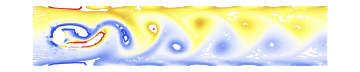

```mathematica
Show[ContourPlot[vorticity[8,x,y],{x,0,2.2},{y,0,0.41},Sequence[AspectRatio->Automatic,ContourShading->None,Contours->cc,ContourStyle->colors,Axes->False,Frame->None]],Sequence[bmesh,ImageSize->Medium]]
```